Pumping power is -10.11dBm.

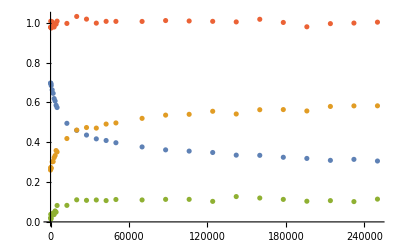

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"optimal_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 5.dBm.

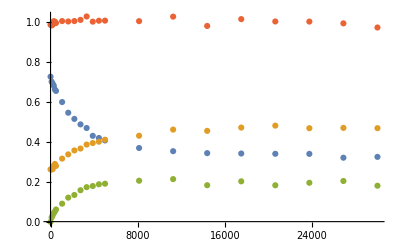

```mathematica
file=path<>"high_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is -25.dBm.

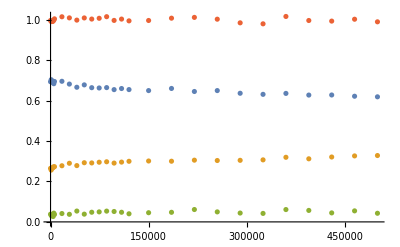

```mathematica
file=path<>"low_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

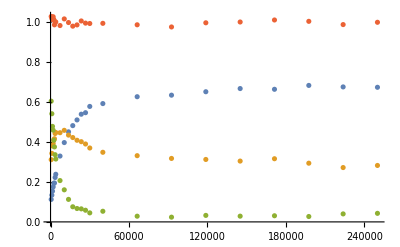

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

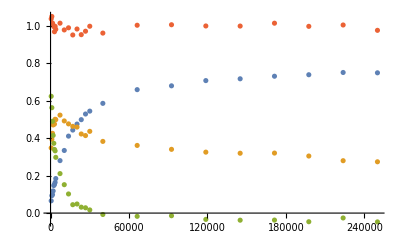

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay_0122.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

{1200.,2960.,4720.,6480.,8240.,10000.,16000.,22000.,28000.,34000.,40000.,82000.,124000.,166000.,208000.,250000.}

Pumping power is 25.dBm.

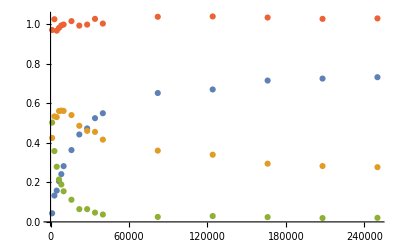

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay_interleaved.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
Time = data["/time"]
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{Time,P0}];
P1toPlot=Transpose[{Time,P1}];
P2toPlot=Transpose[{Time,P2}];
PSumtoPlot=Transpose[{Time,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

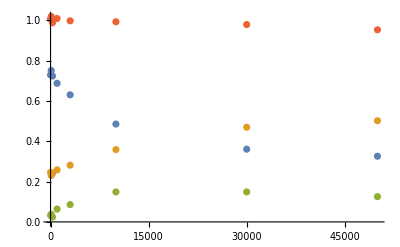

```mathematica
file=path<>"transient_P2_P1_interleaved.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

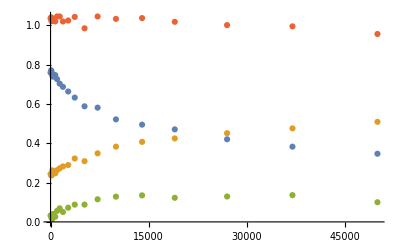

```mathematica
file=path<>"transient_P2_P1_interleaved_more_points.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

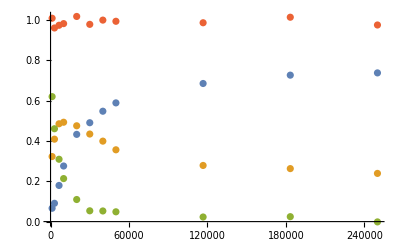

```mathematica
file=path<>"t1_population_2020-02-10-04-07-55.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```